# Boson cloud: metric and scalar field (G = 1)

Notebook version of boson_cloud_tools.wl (package BosonCloud`): the reconstructed metric perturbation h_ab of the boson cloud (traceful ORG plus the ER completion) and the scalar field Φ of the cloud, with derivatives, at any point, from the single output file boson_cloud.wdx of boson_cloud_pipeline_spinscan_lm_slim.wl (one Import for both). Convention: G = 1, G_ab = 8π T_ab, Φ = A Φ_unit (Leaver a_0 = 1, ∫|S|^2 dΩ = 1), cloud mass M_c = 2π ∫ Σ(-T^v_v) dr dχ = A^2 E_cloud, physical metric A^2 (h_ORG + h_comp). Default "Amplitude" -> "Physical"; "Unit" gives per unit A^2. Runs of the older pipelines load from their folder (h_ORG_cloud.wdx and Psi4_Tab_cloud.wdx; 8πG = 1 files are converted).

How to use: Evaluation > Evaluate Notebook (or evaluate the cells of “Definitions” in order, then “Load and self-test” and “Examples”). The definitions span several cells inside one package context: evaluate them in order, from the first. Set dataFile to the boson_cloud.wdx of a run (as given: scan_11725246_l1m1/a_0.80 next to this notebook). Do not give r or χ global values (the stored expressions use these symbols).

## Conventions and formulas

boson_cloud_tools.wl -- the boson cloud: metric perturbation and scalar field in one package (BosonCloud`), reading the single output file
boson_cloud.wdx of boson_cloud_pipeline_spinscan_lm_slim.wl (one Import for both). Merges boson_cloud_metric.wl and boson_cloud_scalar.wl of this
folder (those files are unchanged); all their functions keep their names and options.

Usage
Get["boson_cloud_tools.wl"];
loadCloud["/path/to/run/boson_cloud.wdx"];     (* or loadCloud["/path/to/run"]; older runs: the folder with h_ORG_cloud.wdx and Psi4_Tab_cloud.wdx *)
cloudSelfTest[]                                (* bcmSelfTest[] (metric) and scalarSelfTest[] (field, cloud mass) *)
metric:  hComponent, hCompletion, hTetrad, hCoord, gKerr, gTotal, bcmParameters, bcmSelfTest
field:   phiCloud, phiAbs, phiReal, fRadial, SAngular, rhoCloud, cloudMass, scalarParameters, scalarSelfTest
loadMetric[file], loadScalar[file] still load the separate files of the older pipelines.
cloudDiagnostics[]                             the diagnostics stored in boson_cloud.wdx (the data of plot_boson_cloud.wl)

Convention: G = c = 1, M = 1, G_ab = 8 Pi T_ab, Phi = A Phi_unit (Leaver a_0 = 1, Integral |S|^2 dOmega = 1), A^2 = amp2, cloud mass
M_c = 2 Pi Integral Sigma (-T^v_v) dr dchi = A^2 E_cloud, physical metric perturbation A^2 (h_ORG + h_comp). Files of the 8 Pi G = 1 pipelines are converted
(A^2 = amp2_file/(8 Pi)).

---- boson_cloud_metric.wl ----
boson_cloud_metric.wl -- G = 1 CONVENTION version of Tools/boson_cloud_metric.wl (that file is unchanged).
Convention: G = c = 1, M = 1, G_ab = 8 Pi T_ab (delta G_ab[h] = 8 Pi T_ab), the scalar field is Phi = A Phi_unit (Leaver a_0 = 1, Integral |S|^2 dOmega = 1),
A^2 = amp2, cloud mass M_c = 2 Pi Integral Sigma (-T^v_v) dr dchi; the physical metric perturbation is A^2 (h_ORG + h_comp) with h_ORG, h_comp per unit A^2
(these are the conventions of boson_cloud_pipeline_spinscan_lm.wl and of boson_cloud_scalar.wl in this folder).
Files of the older pipelines (8 Pi G = 1, delta G = T; recognised by the missing params key "einsteinEquation") are converted on loading:
A^2 = amp2_file/(8 Pi) and per-unit values = 8 Pi x the stored ones, so "Unit" means per unit A^2 of the G = 1 convention for every file. The PHYSICAL metric
(the default output) does not depend on the convention: amp2_file h_file is the same for both.
Header of Tools/boson_cloud_metric.wl:
boson_cloud_metric.wl -- evaluate the reconstructed metric perturbation of the boson cloud, and its derivatives, at any (r, chi),
from the spectral data exported by boson_cloud_pipeline_diag.wl (h_ORG_cloud.mx or h_ORG_cloud.wdx).

Usage
Get["boson_cloud_metric.wl"];
loadMetric["/path/to/diag_11688456/h_ORG_cloud.wdx"];      (* or .mx (same Wolfram version / OS only) *)
bcmSelfTest[]                                               (* reference values, coframe, derivatives: run once *)

hComponent["hmbmb", r, chi]              A^2 h_{mbar mbar} (particular ORG solution)
hComponent["hlmb",  r, chi, {i, j}]      d^i/dr^i d^j/dchi^j of A^2 h_{l mbar}
hTetrad[r, chi]                          all tetrad components (ll, lm, lmb, mm, mbmb, mmb), A^2 (h_ORG + h_comp)
hTetrad[r, chi, {i, j}, "Completion" -> False, "Amplitude" -> "Unit"]
hCoord[r, chi, {i, j}]                   coordinate components h_{mu nu}, mu, nu in (v, r, chi, phi)   (4 x 4 matrix)
gKerr[r, chi, {i, j}]                    Kerr background g_{mu nu} (M = 1, a = threshold spin) in the same coordinates
gTotal[r, chi, {i, j}]                   gKerr + A^2 (h_ORG + h_comp)   (the full metric to first order in A^2)

Conventions (as in the pipeline): M = 1; ingoing Kerr coordinates (v, r, chi = cos theta, phi); boosted Kinnersley tetrad
l, n = -d_r, m, mbar; traceful ORG h_{ab} n^b = 0; delta G_ab[h] = 8 Pi T_ab (G = 1). Everything (T_ab, h_ORG, the completion) is per unit
amplitude^2 A^2 of the Leaver normalization, Phi = A Phi_unit; the physical perturbation is A^2 (h_ORG + h_comp)
(A^2 = 3.99e-9/(8 Pi) = 1.589e-10 for the cloud of mass 1e-4 M of diag_11688456). All functions return PHYSICAL values by default;
the option "Amplitude" -> "Unit" (hComponent, hCompletion, hTetrad, hCoord) gives them per unit A^2.
Tetrad components (order l, n, m, mbar):  ll, lm, lmb (= l mbar), mm, mbmb (= mbar mbar), mmb (= m mbar); all n-components vanish.
h_lm = conj(h_lmb), h_mm = conj(h_mbmb) (real metric); h_ll, h_mmb are real.

How each component is rebuilt (same formulas as the pipeline, sections 10, 11, 15):
h_mbmb = sum_l Y_l(chi) [ -4 (r + i a chi)/(r - i a chi)^2 I3_l(r) - 2 (r + i a chi)^2/(r - i a chi)^2 I2_l(r) ],  Y_l = _{-2}Y_{l0};
I2, I3 from their per-panel Chebyshev coefficients for r - r+ < xMax, closed-form (Legendre Q) tails beyond.
h_mmb  = -(1 - chi^2) P(chi)^2 [ K2(r) + 2 r/(r^2 + a^2 chi^2) K3(r) ]  (S = sqrt(1 - chi^2) P); zero beyond xMax (|h| < e^{2 q xMax}).
h_lmb, h_ll: 2D Chebyshev interpolation of the node values (radial panel x chi); h_lmb is interpolated as h_lmb/sin(theta).
Outer region r > rMax: panels in zeta = rMax/r.
Derivatives are exact derivatives of these representations (Chebyshev differentiation, symbolic chain/Leibniz rules), to any order.
Inputs are converted to the working precision of the run (wp = 60 digits): give r, chi as exact numbers or with >= wp digits;
machine numbers are used as exact decimals (SetPrecision). Valid for r >= r+ and -1 <= chi <= 1 (chi-derivatives of h_lmb, which contains
sin(theta), are singular at chi = +-1).

---- boson_cloud_scalar.wl ----
boson_cloud_scalar.wl -- G = 1 CONVENTION version of Tools/boson_cloud_scalar.wl (that file is unchanged).
The scalar field of the boson cloud, Phi(v, r, chi, phi~), from Psi4_Tab_cloud.wdx (or .mx) of a pipeline run (same run as its h_ORG_cloud.wdx).
Companion of boson_cloud_metric.wl in this folder.

Convention (as boson_cloud_pipeline_spinscan_lm.wl and boson_cloud_metric.wl):
G = c = 1, M = 1, G_ab = 8 Pi T_ab,  T_ab = d_a Phi d_b conj(Phi) + d_b Phi d_a conj(Phi) - g_ab (g^cd d_c Phi d_d conj(Phi) + mu^2 |Phi|^2),
Phi = A Phi_unit,  cloud mass M_c = 2 Pi Integral dchi dr Sigma (-T^v_v) = A^2 E_cloud,  physical metric perturbation A^2 (h_ORG + h_comp).
Files of the G = 1 pipeline carry params -> "einsteinEquation" and their amp2 is A^2. Files of the older 8 Pi G = 1 pipelines (no such key; delta G = T,
amp2_file E_cloud,old = M_c with E_cloud,old = (1/4) Integral Sigma (-T^v_v)) are converted: A^2 = amp2_file/(8 Pi). The field is the same either way.

Reads the full Psi4_Tab_cloud.wdx (Leaver series "cL") and the slim one of boson_cloud_pipeline_spinscan_lm_slim.wl ("fPanels": Chebyshev coefficients of
f and its first three r-derivatives on the radial panels of the run; f = 0 beyond xMax, where |f| < e^{q xMax}).

Usage
Get["boson_cloud_scalar.wl"];
loadScalar["/path/to/run/Psi4_Tab_cloud.wdx"];   (* A^2 from adm_charges.tsv in the same folder (converted if needed), or "Amp2" -> A^2 (G = 1) *)
scalarSelfTest[]                                 (* f, S against the stored reference values; cloud mass from Phi = target *)

phiCloud[v, r, chi, phi]            Phi (complex), physical (default) or "Amplitude" -> "Unit" (Phi_unit)
phiAbs[r, chi]                      |Phi| (independent of v and phi~)
phiReal[v, r, chi, phi]             Re Phi (the real field with the same time-averaged T_ab is 2 Re Phi, see Real_scalar_field_derivation)
fRadial[r, d]                       d-th r-derivative of the radial function f (Leaver normalization a_0 = 1, no amplitude), d = 0..3
SAngular[chi, d]                    d-th chi-derivative of S(chi) = sin^m(theta) P(chi), normalized Integral |S|^2 dOmega = 1, d = 0..3
rhoCloud[r, chi]                    energy density -T^v_v of the cloud
cloudMass[]                         2 Pi Integral dchi dr Sigma(-T^v_v)  (= the cloud mass of the run, 1e-4 for BOSON_CLOUDMASS = 1e-4)

The field (M = 1, ingoing Kerr coordinates (v, r, chi = cos theta, phi~), as in the pipelines):
Phi = N e^{-i omega v + i m phi~ + i Theta(r)} f(r) S(chi),   Theta(r) = omega (r + 2 Log[r - r-])   (Theta' = K/Delta at omega = m Omega_H),
f = e^{q r} (r - r-)^(alpha - 1) Sum_n a_n u^n,  u = (r - r+)/(r - r-),  a_0 = 1  (Leaver/Dolan series, real at threshold),
S(chi) = sin^m(theta) P(chi), P the polynomial of the run (BHPToolkit spheroidal harmonic, Integral |S|^2 dOmega = 1).
In Boyer-Lindquist coordinates the same field is N e^{-i omega t + i m phi} f(r) S(theta) (Theta = omega r* - m r#).
Normalization N (option "Amplitude"): "Physical" (default) N = A = Sqrt[A^2];  "Unit" N = 1 (Leaver normalization, per unit A^2).
Checked (reference run diag_11688456, 8 Pi G = 1 file, A^2 = 3.99342375869e-9/(8 Pi) = 1.58893e-10): 2 Pi Integral Sigma(-T^v_v)[Phi_unit] dr dchi
= 8 Pi x 25041.1691928264 (Python/mpmath, 15 digits); the previous version of this tool gave the cloud mass 1.0000000000000000000000046e-4 from the same field.

## Definitions

### Package and usage messages

```mathematica
BeginPackage["BosonCloud`"];

loadMetric::usage = "loadMetric[file] loads h_ORG_cloud.mx or h_ORG_cloud.wdx exported by boson_cloud_pipeline_diag.wl.";
hComponent::usage = "hComponent[comp, r, chi, {i, j}] gives d^i/dr^i d^j/dchi^j of the ORG tetrad component comp (\"hmbmb\", \"hmmb\", \"hlmb\", \"hll\") of the particular solution. {i, j} defaults to {0, 0}. Option \"Amplitude\" -> \"Physical\" (default: times A^2 of the run) or \"Unit\" (per unit A^2).";
hCompletion::usage = "hCompletion[r, chi, {i, j}] gives the completion (ER zero modes with the Komar-fixed amplitudes) as an Association of tetrad components ll, lm, lmb. Option \"Amplitude\" -> \"Physical\" (default) or \"Unit\".";
hTetrad::usage = "hTetrad[r, chi, {i, j}, opts] gives all tetrad components (ll, lm, lmb, mm, mbmb, mmb) of h_ORG + h_comp (options \"Completion\" -> True|False, \"Amplitude\" -> \"Physical\" (default) | \"Unit\").";
hCoord::usage = "hCoord[r, chi, {i, j}, opts] gives the coordinate components h_{mu nu} (mu, nu = v, r, chi, phi) as a 4 x 4 matrix; same options as hTetrad.";
gKerr::usage = "gKerr[r, chi, {i, j}] gives the (i, j) derivative of the Kerr metric g_{mu nu} (M = 1, a = threshold spin) in ingoing coordinates (v, r, chi, phi).";
gTotal::usage = "gTotal[r, chi, {i, j}, opts] gives gKerr + A^2 (h_ORG + h_comp) (option \"Completion\" -> True|False).";
bcmParameters::usage = "bcmParameters[] gives the run parameters, grid sizes and completion data.";
bcmSelfTest::usage = "bcmSelfTest[] checks the rebuilt components against the reference values of the run, the coframe against the stored completion, and the derivatives against finite differences.";
loadScalar::usage = "loadScalar[file, \"Amp2\" -> Automatic | x] loads Psi4_Tab_cloud.wdx (or .mx) of a pipeline run. A^2 (G = 1) is read from adm_charges.tsv in the same folder (converted from 8 Pi G = 1 files), from the loaded metric, or given.";
phiCloud::usage = "phiCloud[v, r, chi, phi, \"Amplitude\" -> \"Physical\" | \"Unit\"] gives the complex scalar field of the cloud (G = 1: Phi = A Phi_unit).";
phiAbs::usage = "phiAbs[r, chi, opts] gives |Phi| (same options as phiCloud).";
phiReal::usage = "phiReal[v, r, chi, phi, opts] gives Re Phi.";
fRadial::usage = "fRadial[r, d] gives the d-th r-derivative (d = 0..3) of the radial function f, Leaver normalization a_0 = 1.";
SAngular::usage = "SAngular[chi, d] gives the d-th chi-derivative (d = 0..3) of S(chi) = sin^m(theta) P(chi), Integral |S|^2 dOmega = 1.";
rhoCloud::usage = "rhoCloud[r, chi, opts] gives the energy density -T^v_v of the cloud (same options as phiCloud).";
cloudMass::usage = "cloudMass[opts] gives 2 Pi Integral dchi dr Sigma(-T^v_v) (\"Physical\": the cloud mass M_c; \"Unit\": E_cloud = M_c/A^2).";
scalarParameters::usage = "scalarParameters[] gives a, mu, omega, m, q, alpha, r+, r-, A^2, the series length and the normalization constants.";
scalarSelfTest::usage = "scalarSelfTest[] compares f and S with the reference values stored by the pipeline and the cloud mass with its target.";
loadCloud::usage = "loadCloud[file] loads boson_cloud.wdx (the single output file of boson_cloud_pipeline_spinscan_lm_slim.wl): the metric (hComponent, hTetrad, hCoord, gTotal, ...) and the scalar field (phiCloud, fRadial, rhoCloud, ...) with one Import. loadCloud[dir] loads boson_cloud.wdx in dir, or, for runs of the older pipelines, h_ORG_cloud.wdx and Psi4_Tab_cloud.wdx in dir. Option \"Amp2\" -> x overrides A^2 (G = 1) of the scalar field.";
cloudSelfTest::usage = "cloudSelfTest[] runs bcmSelfTest[] and scalarSelfTest[].";
cloudDiagnostics::usage = "cloudDiagnostics[] gives the \"diagnostics\" Association of boson_cloud.wdx (what plot_boson_cloud.wl plots), or Missing[] for older files.";
```

### metric (from boson_cloud_metric.wl)

```mathematica
(* ================================================================ metric (from boson_cloud_metric.wl) *)
Begin["`Metric`"];
```

### loading

```mathematica
(* ---------------------------------------------------------------- loading *)
loadMetric[file_String] := Module[{d},
   If[! FileExistsQ[file], Message[loadMetric::nofile, file]; Return[$Failed]];
   If[ValueQ[Global`r] || ValueQ[Global`χ], Message[loadMetric::glob]; Return[$Failed]];
   d = Block[{$Context = "Global`", $ContextPath = {"System`", "Global`"}}, Import[file]];
   If[! AssociationQ[d], Message[loadMetric::bad, file]; Return[$Failed]];
   setup[KeyDrop[d, {"diagnostics", "psi4", "scalar"}]];
   Print["metric from ", file, ":  a = ", N[aN, 15], ",  lmax = ", Max[lList], ",  wp = ", wp, ",  ", nPan, " inner + ", nOut, " outer panels x ", nPn,
     " nodes,  nchi = ", nchi, ",  A^2 = ", N[amp2, 12], " (G = 1)", If[TrueQ[g1File], "", "   [file of the 8 Pi G = 1 pipelines: converted, A^2 = amp2_file/(8 Pi)]"]];
   ];
loadMetric::nofile = "file `1` not found.";
loadMetric::bad = "`1` does not contain the expected Association.";
loadMetric::bcmnl = "no data loaded: call loadMetric[file] first.";
loadMetric::glob = "Global`r or Global`χ has a value; the exported expressions use these symbols. Clear them (Clear[r, χ]) and load again.";

(* the exported expressions (P(chi), the completion modes) contain the coordinates r and chi as symbols. Their context depends on how the file
   was read (Global` or the context current at Import), so they are replaced by NAME, whatever their context *)
rcSub[e_, rv_, cv_] := e /. s_Symbol /; (Context[s] =!= "System`" && MemberQ[{"r", "χ"}, SymbolName[s]]) :> If[SymbolName[s] === "r", rv, cv];

setup[d_] := Module[{g = d["grid"], p = d["params"]},
   dat = d;
   wp = p["wp"]; aN = p["a"]; rp = p["rplus"];
   kap = Sqrt[1 - aN^2];
   xB = g["xB"]; xMax = g["xMax"]; nPn = g["nPn"]; nchi = g["nchi"]; zB = g["zetaB"];
   nPan = Length[xB] - 1; nOut = Length[zB] - 1; rMax = rp + xMax;
   chiN = g["chiNodes"]; sN = Sqrt[1 - chiN^2];
   lList = d["hmbmb"]["lList"];
   I123 = d["hmbmb"]["I123"]; gC = d["hmbmb"]["g"]; Cup = d["hmbmb"]["Cup"];
   K123 = d["hmmb"]["K123"]; tauC = d["hmmb"]["tau"];
   Ppoly = Function[Evaluate[rcSub[d["hmmb"]["PpolyR"], 0, #]]];
   nodes["hlmb"] = {d["hlmb"]["inner"], d["hlmb"]["outer"]};
   nodes["hll"] = {d["hll"]["inner"], d["hll"]["outer"]};
   comp = d["completion"]; {cM, cA} = comp["coefficients"];
   (* convention of the file: G = 1 (params key "einsteinEquation") or the older 8 Pi G = 1 (delta G = T); conv converts the stored per-unit values to G = 1 *)
   g1File = KeyExistsQ[d["params"], "einsteinEquation"]; conv = If[g1File, 1, 8 Pi];
   ampFile = comp["amp2"];                            (* the file's own amplitude: ampFile h_file = physical metric *)
   amp2 = ampFile/conv;                               (* A^2 of the G = 1 convention: Phi = Sqrt[amp2] Phi_unit, delta G = 8 Pi T *)
   cache = <||>;                                       (* cached coefficient matrices and derivative formulas of this data set *)
   loaded = True;
   ];
loaded = False; cache = <||>;
SetAttributes[memo, HoldRest];
memo[key_, expr_] := If[KeyExistsQ[cache, key], cache[key], cache[key] = expr];
check[] := If[TrueQ[loaded], True, Message[loadMetric::bcmnl]; Abort[]];
```

### numbers and Chebyshev utilities (as in the pipeline)

```mathematica
(* ---------------------------------------------------------------- numbers and Chebyshev utilities (as in the pipeline) *)
toWP[x_] := Which[Precision[x] === Infinity, N[x, wp], Precision[x] === MachinePrecision, SetPrecision[x, wp], True, x];
chebMat[nn_] := memo[{"chebMat", nn}, N[Table[(2/nn) If[k == 0, 1/2, 1] Cos[k Pi (j + 1/2)/nn], {k, 0, nn - 1}, {j, 0, nn - 1}], wp]];
chebDer[c_List] := Module[{nn = Length[c] - 1, dd},                    (* coefficients of df/dz *)
   dd = ConstantArray[0, nn + 2];
   Do[dd[[k]] = dd[[k + 2]] + 2 k c[[k + 1]], {k, nn, 1, -1}];
   dd[[1]] = dd[[1]]/2; Take[dd, nn + 1]];
chebEval[c_List, z_] := c . ChebyshevT[Range[0, Length[c] - 1], z];
panelIndex[x_] := Min[nPan, Max[1, LengthWhile[xB, # <= x &]]];
panMid[p_] := (xB[[p]] + xB[[p + 1]])/2; panH[p_] := (xB[[p + 1]] - xB[[p]])/2;
zMid[q_] := (zB[[q]] + zB[[q + 1]])/2; zH[q_] := (zB[[q + 1]] - zB[[q]])/2;
(* d-th r-derivative of a panel-wise Chebyshev function (inner region) *)
panelEval[coefs_, r0_, d_] := Module[{x = r0 - rp, p, t},
   p = panelIndex[x]; t = (x - panMid[p])/panH[p];
   chebEval[Nest[chebDer, coefs[[p]], d], t]/panH[p]^d];
```

### spin-weighted harmonics _{-2}Y_{l0} and chi-derivatives

```mathematica
(* ---------------------------------------------------------------- spin-weighted harmonics _{-2}Y_{l0} and chi-derivatives
   Y_l = N_l (1 - chi^2) P_l''(chi), N_l = sqrt((2l+1)(l-2)!/(4 pi (l+2)!)) (sign convention of SpinWeightedSphericalHarmonicY);
   P_l^{(k)} = (2k-1)!! C^{(k+1/2)}_{l-k} (Gegenbauer) *)
Pder[l_, k_, c_] := If[k > l, 0, (2 k - 1)!! GegenbauerC[l - k, k + 1/2, c]];
Nl[l_] := Sqrt[(2 l + 1) (l - 2)!/(4 Pi (l + 2)!)];
Yd[l_, m_, c_] := N[Nl[l], wp] ((1 - c^2) Pder[l, m + 2, c] - 2 m c Pder[l, m + 1, c] - m (m - 1) Pder[l, m, c]);     (* d^m/dchi^m of (1 - chi^2) P'' *)
```

### h_mbarmbar

```mathematica
(* ---------------------------------------------------------------- h_mbarmbar *)
(* closed-form tails beyond r+ + xMax: I_k^{(d)}(r) = Cup NUp kappa^{-d} F_k^{(d)}(X), X = (r - 1)/kappa *)
QH[l_, X_] := Sqrt[Pi] Gamma[l + 1]/(Gamma[l + 3/2] (2 X)^(l + 1)) Hypergeometric2F1[(l + 1)/2, (l + 2)/2, l + 3/2, 1/X^2];
NUp[l_] := (2 l + 1)!!/((l + 2)! kap^(l + 3));
tailF[l_, k_, d_] := memo[{"tail", l, k, d}, Module[{X, F},
   F = Switch[k, 0, D[QH[l, X], {X, 2}], 1, -kap D[QH[l, X], X], 2, kap^2 QH[l, X], 3, kap^3 (QH[l - 1, X] - QH[l + 1, X])/(2 l + 1)];
   Function[Evaluate[{X}], Evaluate[Cup[l] NUp[l] kap^-d D[F, {X, d}]]]]];
Ival[l_, k_, d_, r0_] := If[r0 - rp >= xMax, tailF[l, k, d][(r0 - 1)/kap],
   panelEval[If[k == 0, gC[l], I123[l][[All, k]]], r0, d]];
(* symbolic (i, j)-derivative of one mode, linear in i2[n] = I2^{(n)}, i3[n] = I3^{(n)}, y[m] = Y^{(m)} *)
hmbD[i_, j_] := memo[{"hmb", i, j}, Module[{rr, cc, I2f, I3f, Yf, e},
   e = Yf[cc] (-4 (rr + I aN cc)/(rr - I aN cc)^2 I3f[rr] - 2 (rr + I aN cc)^2/(rr - I aN cc)^2 I2f[rr]);
   e = D[e, {rr, i}, {cc, j}] /. {Derivative[n_][I3f][rr] :> i3[n], I3f[rr] :> i3[0], Derivative[n_][I2f][rr] :> i2[n], I2f[rr] :> i2[0],
       Derivative[m_][Yf][cc] :> y[m], Yf[cc] :> y[0]};
   Function[Evaluate[{rr, cc}], Evaluate[e]]]];
hmbmb[r0_, c0_, {i_, j_}] := Module[{e = hmbD[i, j][r0, c0]},
   Sum[e /. {i3[n_] :> Ival[l, 3, n, r0], i2[n_] :> Ival[l, 2, n, r0], y[m_] :> Yd[l, m, c0]}, {l, lList}]];
```

### h_mmbar

```mathematica
(* ---------------------------------------------------------------- h_mmbar *)
hmmD[i_, j_] := memo[{"hmm", i, j}, Module[{rr, cc, K2f, K3f, e},
   e = -(1 - cc^2) Ppoly[cc]^2 (K2f[rr] + 2 rr/(rr^2 + aN^2 cc^2) K3f[rr]);
   e = D[e, {rr, i}, {cc, j}] /. {Derivative[n_][K3f][rr] :> k3[n], K3f[rr] :> k3[0], Derivative[n_][K2f][rr] :> k2[n], K2f[rr] :> k2[0]};
   Function[Evaluate[{rr, cc}], Evaluate[e]]]];
hmmb[r0_, c0_, {i_, j_}] := If[r0 - rp >= xMax, 0 r0,
   hmmD[i, j][r0, c0] /. {k2[n_] :> panelEval[K123[[All, 2]], r0, n], k3[n_] :> panelEval[K123[[All, 3]], r0, n]}];
```

### h_lmbar, h_ll: 2D Chebyshev interpolation of the node values

```mathematica
(* ---------------------------------------------------------------- h_lmbar, h_ll: 2D Chebyshev interpolation of the node values *)
(* coefficient matrix [[t-index, chi-index]] of the panel, differentiated i times in t and j times in chi (cached) *)
c2Cache[cname_, reg_, p_, i_, j_] := memo[{"c2", cname, reg, p, i, j}, Which[
   i > 0, Transpose[chebDer /@ Transpose[c2Cache[cname, reg, p, i - 1, j]]],
   j > 0, chebDer /@ c2Cache[cname, reg, p, i, j - 1],
   True, Module[{V = nodes[cname][[If[reg === "in", 1, 2], p]]},
     If[cname === "hlmb", V = (#/sN) & /@ V];          (* spin weight -1: interpolate h/sin(theta) *)
     chebMat[nPn] . V . Transpose[chebMat[nchi]]]]];
(* d^n/dr^n of F(t(r)) on the outer panels, t = (rMax/r - zm)/zh: coefficients of F^{(k)}(t), k = 0..n *)
chainOuter[n_] := chainOuter[n] = Module[{rr, zm, zh, rM, F, e},          (* data independent *)
   e = D[F[(rM/rr - zm)/zh], {rr, n}] /. {Derivative[k_][F][_] :> fd[k], F[_] :> fd[0]};
   Function[Evaluate[{rr, zm, zh, rM}], Evaluate[Table[Coefficient[e, fd[k]], {k, 0, n}]]]];
sinD[k_, c_] := D[Sqrt[1 - cc^2], {cc, k}] /. cc -> c;
(* (i, j)-derivative of Q = h / sin^sw(theta) in the panel variables, then the r chain rule; the sin(theta) factor by Leibniz in chi *)
interpQ[cname_, r0_, c0_, i_, jq_] := Module[{x = r0 - rp, p, q, t, z0, co, Tt, Tc},
   Tc = ChebyshevT[Range[0, nchi - 1], c0];
   If[x < xMax,
    p = panelIndex[x]; t = (x - panMid[p])/panH[p]; Tt = ChebyshevT[Range[0, nPn - 1], t];
    (Tt . c2Cache[cname, "in", p, i, jq] . Tc)/panH[p]^i,
    z0 = rMax/r0; q = Min[nOut, Max[1, LengthWhile[zB, # <= z0 &]]]; t = (z0 - zMid[q])/zH[q]; Tt = ChebyshevT[Range[0, nPn - 1], t];
    co = chainOuter[i][r0, zMid[q], zH[q], rMax];
    Sum[co[[k + 1]] (Tt . c2Cache[cname, "out", q, k, jq] . Tc), {k, 0, i}]]];
hInterp[cname_, r0_, c0_, {i_, j_}] := If[cname === "hlmb",
   Sum[Binomial[j, m] sinD[j - m, c0] interpQ[cname, r0, c0, i, m], {m, 0, j}],
   interpQ[cname, r0, c0, i, j]];
```

### public: ORG components

```mathematica
(* ---------------------------------------------------------------- public: ORG components *)
(* amplitude factor: "Physical" (default) = A^2 of the run (cloud mass BOSON_CLOUDMASS), "Unit" = per unit A^2 of the G = 1 convention (Leaver normalization, Phi = A Phi_unit) *)
ampF[a_] := Switch[a, "Physical", ampFile, "Unit", conv, _, Message[hComponent::amp, a]; Abort[]];          (* ampFile h_file = A^2 h (G = 1); conv h_file = h per unit A^2 (G = 1) *)
hComponent::amp = "\"Amplitude\" must be \"Physical\" or \"Unit\", not `1`.";
Options[hComponent] = {"Amplitude" -> "Physical"};
hComponent[cname_String, r0_?NumericQ, c0_?NumericQ, ij : {_Integer?NonNegative, _Integer?NonNegative} : {0, 0}, OptionsPattern[]] :=
  (check[]; ampF[OptionValue["Amplitude"]] hComp0[cname, r0, c0, ij]);
(* per unit A^2 *)
hComp0[cname_String, r0_?NumericQ, c0_?NumericQ, {i_Integer?NonNegative, j_Integer?NonNegative}] := (check[];
   With[{rr = toWP[r0], cc = toWP[c0]},
    Switch[cname,
     "hmbmb", hmbmb[rr, cc, {i, j}],
     "hmmb", hmmb[rr, cc, {i, j}],
     "hlmb" | "hll", hInterp[cname, rr, cc, {i, j}],
     "hmm", Conjugate[hmbmb[rr, cc, {i, j}]],
     "hlm", Conjugate[hInterp["hlmb", rr, cc, {i, j}]],
     _, Message[hComponent::comp, cname]; $Failed]]);
hComponent::comp = "unknown component `1`; use \"hmbmb\", \"hmmb\", \"hlmb\", \"hll\" (or \"hmm\", \"hlm\").";
```

### completion (closed form)

```mathematica
(* ---------------------------------------------------------------- completion (closed form) *)
compD[which_, i_, j_] := memo[{"comp", which, i, j}, Module[{rr, cc, e},
   e = rcSub[comp[which], rr, cc];
   Function[Evaluate[{rr, cc}], Evaluate[D[e, {rr, i}, {cc, j}]]]]];
Options[hCompletion] = {"Amplitude" -> "Physical"};
hCompletion[r0_?NumericQ, c0_?NumericQ, ij : {_Integer?NonNegative, _Integer?NonNegative} : {0, 0}, OptionsPattern[]] :=
  (check[]; Map[ampF[OptionValue["Amplitude"]] # &, hCompletion0[r0, c0, ij]]);
(* per unit A^2 *)
hCompletion0[r0_?NumericQ, c0_?NumericQ, {i_Integer?NonNegative, j_Integer?NonNegative}] := (check[];
   With[{rr = toWP[r0], cc = toWP[c0]},
    AssociationThread[{"ll", "lm", "lmb"}, cM compD["tetrad_ER_unit_dM", i, j][rr, cc] + cA compD["tetrad_ER_unit_da", i, j][rr, cc]]]);
```

### all tetrad components

```mathematica
(* ---------------------------------------------------------------- all tetrad components *)
Options[hTetrad] = {"Completion" -> True, "Amplitude" -> "Physical"};
hTetrad[r0_?NumericQ, c0_?NumericQ, ij : {_Integer?NonNegative, _Integer?NonNegative} : {0, 0}, OptionsPattern[]] := Module[{lmb, mbmb, h, hc, s},
   check[];
   lmb = hComp0["hlmb", r0, c0, ij]; mbmb = hComp0["hmbmb", r0, c0, ij];
   h = <|"ll" -> hComp0["hll", r0, c0, ij], "lm" -> Conjugate[lmb], "lmb" -> lmb, "mm" -> Conjugate[mbmb], "mbmb" -> mbmb,
     "mmb" -> hComp0["hmmb", r0, c0, ij]|>;
   If[TrueQ[OptionValue["Completion"]], hc = hCompletion0[r0, c0, ij];
    h = <|"ll" -> h["ll"] + hc["ll"], "lm" -> h["lm"] + hc["lm"], "lmb" -> h["lmb"] + hc["lmb"], "mm" -> h["mm"], "mbmb" -> h["mbmb"], "mmb" -> h["mmb"]|>];
   s = ampF[OptionValue["Amplitude"]];
   Map[s # &, h]];
```

### background: Kerr metric and the coframe (pipeline section 1, M = 1)

```mathematica
(* ---------------------------------------------------------------- background: Kerr metric and the coframe (pipeline section 1, M = 1) *)
bgSym := memo[{"bg"}, Module[{rr, cc, a = aN, gdd, lu, nu, mu, mbu, eDu, eDd, eta},
   gdd = {{-(1 - (2 rr)/(rr^2 + a^2 cc^2)), 1, 0, -(2 a rr (1 - cc^2))/(rr^2 + a^2 cc^2)},
     {1, 0, 0, -a (1 - cc^2)},
     {0, 0, (rr^2 + a^2 cc^2)/(1 - cc^2), 0},
     {-(2 a rr (1 - cc^2))/(rr^2 + a^2 cc^2), -a (1 - cc^2), 0, (1 - cc^2) (rr^2 + a^2 + (2 a^2 rr (1 - cc^2))/(rr^2 + a^2 cc^2))}};
   lu = {(rr^2 + a^2)/(rr^2 + a^2 cc^2), (rr^2 - 2 rr + a^2)/(2 (rr^2 + a^2 cc^2)), 0, a/(rr^2 + a^2 cc^2)};
   nu = {0, -1, 0, 0};
   mu = 1/(Sqrt[2] (rr + I a cc)) {I a Sqrt[1 - cc^2], 0, -Sqrt[1 - cc^2], I/Sqrt[1 - cc^2]};
   mbu = 1/(Sqrt[2] (rr - I a cc)) {-I a Sqrt[1 - cc^2], 0, -Sqrt[1 - cc^2], -I/Sqrt[1 - cc^2]};       (* conj(m) for real r, chi, a *)
   eDu = {lu, nu, mu, mbu};
   eDd = eDu . gdd;                                     (* e_{a mu} = g_{mu nu} e_a^nu *)
   eta = {{0, -1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}};
   {rr, cc, gdd, Inverse[eta] . eDd}]];                 (* coframe omega^a_mu = eta^{ab} e_{b mu} *)
frameD[i_, j_] := memo[{"frame", i, j}, With[{b = bgSym}, Function[Evaluate[{b[[1]], b[[2]]}], Evaluate[D[b[[4]], {b[[1]], i}, {b[[2]], j}]]]]];
kerrD[i_, j_] := memo[{"kerr", i, j}, With[{b = bgSym}, Function[Evaluate[{b[[1]], b[[2]]}], Evaluate[D[b[[3]], {b[[1]], i}, {b[[2]], j}]]]]];
gKerr[r0_?NumericQ, c0_?NumericQ, {i_Integer?NonNegative, j_Integer?NonNegative}] := (check[]; kerrD[i, j][toWP[r0], toWP[c0]]);
gKerr[r0_?NumericQ, c0_?NumericQ] := gKerr[r0, c0, {0, 0}];

hTetMat[h_] := {{h["ll"], 0, h["lm"], h["lmb"]}, {0, 0, 0, 0}, {h["lm"], 0, h["mm"], h["mmb"]}, {h["lmb"], 0, h["mmb"], h["mbmb"]}};   (* order l, n, m, mbar *)
(* h_{mu nu} = omega^a_mu h_ab omega^b_nu; derivatives by the Leibniz rule over the three factors *)
Options[hCoord] = Options[hTetrad];
hCoord[r0_?NumericQ, c0_?NumericQ, {i_Integer?NonNegative, j_Integer?NonNegative}, opts : OptionsPattern[]] := Module[{rr = toWP[r0], cc = toWP[c0], H, W},
   check[];
   H[a1_, b1_] := H[a1, b1] = hTetMat[hTetrad[rr, cc, {a1, b1}, opts]];
   W[a1_, b1_] := W[a1, b1] = frameD[a1, b1][rr, cc];
   Sum[Multinomial[i1, i2, i - i1 - i2] Multinomial[j1, j2, j - j1 - j2] Transpose[W[i1, j1]] . H[i2, j2] . W[i - i1 - i2, j - j1 - j2],
    {i1, 0, i}, {i2, 0, i - i1}, {j1, 0, j}, {j2, 0, j - j1}]];
hCoord[r0_?NumericQ, c0_?NumericQ, opts : OptionsPattern[]] := hCoord[r0, c0, {0, 0}, opts];

Options[gTotal] = {"Completion" -> True};
gTotal[r0_?NumericQ, c0_?NumericQ, ij : {_Integer?NonNegative, _Integer?NonNegative} : {0, 0}, OptionsPattern[]] :=
  gKerr[r0, c0, ij] + hCoord[r0, c0, ij, "Completion" -> OptionValue["Completion"], "Amplitude" -> "Physical"];

bcmParameters[] := (check[]; <|"params" -> dat["params"], "rplus" -> rp, "xMax" -> xMax, "rMax" -> rMax, "innerPanels" -> nPan, "outerPanels" -> nOut,
    "nodesPerPanel" -> nPn, "nchi" -> nchi, "lList" -> lList, "amp2" -> amp2, "amp2File" -> ampFile, "fileConvention" -> If[TrueQ[g1File], "G = 1 (delta G = 8 Pi T)", "8 Pi G = 1 (delta G = T), converted"],
    "completionCoefficients" -> conv {cM, cA},
    "totalMass" -> comp["totalMass"], "totalAngularMomentum" -> comp["totalAngularMomentum"], "conventions" -> dat["conventions"]|>);
```

### self-test

```mathematica
(* ---------------------------------------------------------------- self-test *)
relE[x_, y_] := Abs[x - y]/Max[Abs[y], 10^-300];
(* a computed difference is either a number or a zero of significance arithmetic (0``k, i.e. below 10^-k): print it as such *)
fmt[x_] := Which[! NumericQ[x], "NOT NUMERIC", x == 0, If[Accuracy[x] === Infinity, "0", "< 1e-" <> ToString[Floor[Accuracy[x]]]],
   True, Module[{e = Floor[Log10[Abs[N[x]]]]}, ToString[NumberForm[N[x/10^e], {3, 2}]] <> "e" <> ToString[e]]];
passQ[x_, tol_] := NumericQ[x] && If[x == 0, Accuracy[x] === Infinity || Accuracy[x] > -Log10[N[tol]], x < tol];
bcmSelfTest[] := Module[{ref, res, pts, eps, ok = True, e, w, cr},
   check[];
   (* 1. reference values stored by the pipeline *)
   ref = dat["reference"];
   Print["1. reference values of the run (relative difference):"];
   Do[res = Table[relE[hComp0[c, pt["r"], pt["chi"], {0, 0}], pt[c]], {c, {"hmbmb", "hmmb", "hlmb", "hll"}}];
    Print["   (r, chi) = (", NumberForm[N[pt["r"]], 9], ", ", NumberForm[N[pt["chi"]], 4], "):  hmbmb ", fmt[res[[1]]], ",  hmmb ", fmt[res[[2]]],
     ",  hlmb ", fmt[res[[3]]], ",  hll ", fmt[res[[4]]]];
    If[! AllTrue[res, passQ[#, 10^-25] &], ok = False], {pt, ref}];
   (* 2. coframe: tetrad -> coordinates of the ER zero modes vs the coordinate components stored by the pipeline *)
   e = Max[Table[Module[{t = tc[[1]], c = tc[[2]], tet, crd, W0},
       tet = rcSub[comp[t], 37/10, 3/10]; crd = rcSub[comp[c], 37/10, 3/10]; W0 = frameD[0, 0][N[37/10, wp], N[3/10, wp]];
       Max[Abs[Flatten[N[Transpose[W0] . hTetMat[<|"ll" -> tet[[1]], "lm" -> tet[[2]], "lmb" -> tet[[3]], "mm" -> 0, "mbmb" -> 0, "mmb" -> 0|>] . W0 - crd, wp]]]]/
        Max[Abs[Flatten[N[crd, wp]]]]], {tc, {{"tetrad_ER_unit_dM", "coord_ER_unit_dM"}, {"tetrad_ER_unit_da", "coord_ER_unit_da"}}}]];
   Print["2. coframe: omega^T h_tetrad omega of the ER modes = stored coordinate components (relative difference):  ", fmt[e]];
   If[! passQ[e, 10^-25], ok = False];
   (* 3. derivatives vs central finite differences; steps 10^-10 in chi and 10^-10 max(1, r - r+) in r: truncation error <~ 10^-14 relative
      (panel width ~ 10^-3 at the innermost point), round-off of the 2nd differences ~ 10^-17 with the ~37 significant digits of h_ll;
      points inside panels, inner and outer region *)
   eps = N[10^-10, wp];
   pts = {{rp + 3/1000, 21/100}, {37/10, -3/10}, {12, 7/10}, {150, 1/3}, {5000, 21/100}};
   Print["3. derivatives vs finite differences (max relative difference over the points; h_mmbar only inside rMax):"];
   Do[Module[{dr, dc, drr, dcc, drc},
      w = Select[pts, c =!= "hmmb" || #[[1]] - rp < xMax &];
      {dr, dc, drr, dcc, drc} = Max /@ Transpose[Table[Module[{r0 = N[pt[[1]], wp], c0 = N[pt[[2]], wp], f, er},
          er = eps Max[1, r0 - rp];
          f[a1_, b1_] := hComp0[c, r0 + a1 er, c0 + b1 eps, {0, 0}];
          {relE[hComp0[c, r0, c0, {1, 0}], (f[1, 0] - f[-1, 0])/(2 er)],
           relE[hComp0[c, r0, c0, {0, 1}], (f[0, 1] - f[0, -1])/(2 eps)],
           relE[hComp0[c, r0, c0, {2, 0}], (f[1, 0] - 2 f[0, 0] + f[-1, 0])/er^2],
           relE[hComp0[c, r0, c0, {0, 2}], (f[0, 1] - 2 f[0, 0] + f[0, -1])/eps^2],
           relE[hComp0[c, r0, c0, {1, 1}], (f[1, 1] - f[1, -1] - f[-1, 1] + f[-1, -1])/(4 er eps)]}], {pt, w}]];
      Print["   ", c, ":  d_r ", fmt[dr], ",  d_chi ", fmt[dc], ",  d_r^2 ", fmt[drr], ",  d_chi^2 ", fmt[dcc], ",  d_r d_chi ", fmt[drc]];
      If[! AllTrue[{dr, dc, drr, dcc, drc}, passQ[#, 10^-10] &], ok = False]], {c, {"hmbmb", "hmmb", "hlmb", "hll"}}];
   (* 4. spectral d_r of h_lmbar, h_ll at the nodes vs the d_r values stored by the pipeline (from the ODE solution); slim files do not store them *)
   If[KeyExistsQ[dat["hlmb"], "drInner"],
   cr = Max[Table[Module[{p = pp, j = 7, V, r0},
       r0 = rp + panMid[p] + panH[p] Cos[Pi (j - 1/2)/nPn];
       V = dat[c]["drInner"][[p, j]];
       Max[Table[relE[hComp0[c, r0, chiN[[k]], {1, 0}], V[[k]]], {k, {5, Ceiling[nchi/2], nchi - 5}}]]], {c, {"hlmb", "hll"}}, {pp, {1, 30, Ceiling[nPan/2], nPan}}]];
   Print["4. spectral d_r of h_lmbar, h_ll at nodes vs the stored d_r (ODE):  ", fmt[cr]];
   If[! passQ[cr, 10^-20], ok = False],
    Print["4. spectral d_r of h_lmbar, h_ll vs stored d_r: skipped (slim file without stored d_r)"]];
   (* 5. completion: numeric at a test point, and hTetrad - hTetrad(no completion) = hCompletion *)
   e = Module[{hc = hCompletion[3, 1/2, "Amplitude" -> "Unit"], d1 = hTetrad[3, 1/2, "Amplitude" -> "Unit"], d0 = hTetrad[3, 1/2, "Completion" -> False, "Amplitude" -> "Unit"]},
      If[! AllTrue[Values[hc], NumericQ], "NOT NUMERIC", Max[Table[relE[d1[k] - d0[k], hc[k]], {k, {"ll", "lm", "lmb"}}]]]];
   Print["5. completion at (r, chi) = (3, 1/2), per unit A^2: ", N[hCompletion[3, 1/2, "Amplitude" -> "Unit"], 12],
    ";  hTetrad with - without completion vs hCompletion: ", fmt[e]];
   If[! passQ[e, 10^-30], ok = False];
   Print["6. completion (c_M, c_a) per unit A^2 (G = 1) = ", N[conv {cM, cA}, 12], ",  A^2 = ", N[amp2, 12], ",  total mass = ", N[comp["totalMass"], 12],
    ",  total J = ", N[comp["totalAngularMomentum"], 12]];
   Print[If[ok, "SELF-TEST PASSED", "SELF-TEST: SOME DIFFERENCES ABOVE THE EXPECTED LEVEL (see above)"]];
   ok];
End[];
```

### scalar field (from boson_cloud_scalar.wl)

```mathematica
(* ================================================================ scalar field (from boson_cloud_scalar.wl) *)
Begin["`Scalar`"];
loaded = False;
loadScalar::nofile = "file `1` not found.";
loadScalar::bad = "`1` does not contain the expected Association (boson_cloud.wdx or Psi4_Tab_cloud.wdx).";
loadScalar::amp = "A^2 not found (no adm_charges.tsv next to the file): give it as \"Amp2\" -> value. Only \"Amplitude\" -> \"Unit\" works until then.";
loadScalar::nl = "no data loaded: call loadScalar[file] first.";
loadScalar::glob = "Global`r or Global`χ has a value; the exported polynomial P uses these symbols. Clear them (Clear[r, χ]) and load again.";
check[] := If[TrueQ[loaded], True, Message[loadScalar::nl]; Abort[]];

(* the exported polynomial P(chi) contains chi as a symbol; its context depends on how the file was read: replaced by NAME *)
cSub[e_, cv_] := e /. s_Symbol /; (Context[s] =!= "System`" && SymbolName[s] === "χ") :> cv;

Options[loadScalar] = {"Amp2" -> Automatic};
(* loadScalar[file]: Psi4_Tab_cloud.wdx/.mx (full or slim) or boson_cloud.wdx; the data part is setupScalar (also used by loadCloud) *)
loadScalar[file_String, OptionsPattern[]] := Module[{d},
   If[! FileExistsQ[file], Message[loadScalar::nofile, file]; Return[$Failed]];
   If[ValueQ[Global`r] || ValueQ[Global`χ], Message[loadScalar::glob]; Return[$Failed]];
   d = Block[{$Context = "Global`", $ContextPath = {"System`", "Global`"}}, Import[file]];
   setupScalar[d, file, OptionValue["Amp2"]]];
setupScalar[d_, file_, amp2opt_] := Module[{p, cl, tsv, row, ampStored = Missing[]},
   Which[
    AssociationQ[d] && KeyExistsQ[d, "params"] && KeyExistsQ[d, "scalar"],          (* boson_cloud.wdx *)
     cl = d["scalar"]["cloud"]; If[KeyExistsQ[d, "completion"], ampStored = d["completion"]["amp2"]],
    AssociationQ[d] && KeyExistsQ[d, "params"] && KeyExistsQ[d, "cloud"],           (* Psi4_Tab_cloud.wdx *)
     cl = d["cloud"],
    True, Message[loadScalar::bad, file]; Return[$Failed]];
   p = d["params"];
   wp = p["wp"]; aN = p["a"]; muN = p["mu"]; omN = p["omegac"]; qN = p["q"]; alN = p["alpha"]; rp = p["rplus"]; rm = p["rminus"];
   mM = If[KeyExistsQ[p, "m"], p["m"], 1]; lL = If[KeyExistsQ[p, "l"], p["l"], 1];
   (* radial function: the Leaver series a_n ("cL", full files) or its Chebyshev coefficients on the radial panels ("fPanels", slim files) *)
   fMode = If[KeyExistsQ[cl, "cL"], "series", "panels"];
   If[fMode === "series", cL = cl["cL"],
    cL = {}; fpXB = cl["fPanels"]["xB"]; fpXMax = cl["fPanels"]["xMax"]; fpCoef = cl["fPanels"]["coef"]; fpN = Length[fpXB] - 1];
   Ppoly = Function[Evaluate[cSub[cl["PpolyR"], #]]];
   refVals = Which[KeyExistsQ[d, "scalar"], Lookup[d["scalar"], "reference", {}], KeyExistsQ[d, "reference"], d["reference"], True, {}];
   (* truncation of the series as in the pipeline: |a_n| u^n < 10^-(wp+10) (machine-precision logs only decide where to stop) *)
   If[fMode === "series", logA = N[Log[Abs[cL] + 10^-(3 wp)]]; tailMaxLog = Reverse[FoldList[Max, Reverse[logA]]]];
   (* convention of the file: G = 1 (params key "einsteinEquation") or the older 8 Pi G = 1; conv = amp2_file/A^2 *)
   g1File = KeyExistsQ[p, "einsteinEquation"]; conv = If[g1File, 1, 8 Pi];
   (* A^2 (G = 1): given, or the "amp2" line of adm_charges.tsv (read as text: 25 digits; divided by conv), or the loaded metric of this folder *)
   amp2 = Which[
     NumericQ[amp2opt], amp2opt,
     ! MissingQ[ampStored], ampStored/conv,                                     (* boson_cloud.wdx: the completion's amp2 *)
     StringQ[file] && FileExistsQ[file] && FileExistsQ[tsv = FileNameJoin[{DirectoryName[ExpandFileName[file]], "adm_charges.tsv"}]],
       row = SelectFirst[StringSplit[#, "\t"] & /@ ReadList[tsv, String], Length[#] >= 2 && #[[1]] === "amp2" &, Missing[]];
       If[MissingQ[row], Missing[], ToExpression[StringReplace[row[[2]], {"e" -> "*^", "E" -> "*^"}]]/conv],
     TrueQ[BosonCloud`Metric`loaded], BosonCloud`bcmParameters[]["amp2"],         (* the metric loaded in this session *)
     True, Missing[]];
   If[MissingQ[amp2], Message[loadScalar::amp]];
   (* jets of f (symbolic prefactor, numeric series) and of S = sin^m P (exact polynomial form), rebuilt for every data set *)
   fJetFun = Module[{x0, Rf, sym},
     sym = Table[D[Exp[qN x0] (x0 - rm)^(alN - 1) Rf[(x0 - rp)/(x0 - rm)], {x0, k}], {k, 0, 3}];
     Function[Evaluate[{x0, R0, R1, R2, R3}], Evaluate[sym /. {Derivative[k_][Rf][_] :> {R1, R2, R3}[[k]], Rf[_] :> R0}]]];
   SJetFun = Module[{y}, Function[Evaluate[{y}], Evaluate[Table[D[(1 - y^2)^(mM/2) Ppoly[y], {y, k}], {k, 0, 3}]]]];
   fCache = <||>; loaded = True;
   Print["scalar field from ", file, ":  a = ", N[aN, 15], ",  mu = ", N[muN, 15], ",  omega = m Omega_H = ", N[omN, 15], ",  (l, m) = (", lL, ", ", mM, "),  ",
     If[fMode === "series", ToString[Length[cL]] <> " series terms", "f from " <> ToString[fpN] <> " Chebyshev panels (slim file)"], ",  A^2 = ", If[MissingQ[amp2], "not set", N[amp2, 12]], " (G = 1)", If[g1File, "", "   [file of the 8 Pi G = 1 pipelines: A^2 = amp2_file/(8 Pi)]"]];
   ];
```

### radial function f and its first three r-derivatives

```mathematica
(* ---------------------------------------------------------------- radial function f and its first three r-derivatives *)
toWP[x_] := Which[Precision[x] === Infinity, N[x, wp], Precision[x] === MachinePrecision, SetPrecision[x, wp], True, x];
nOfu[u_] := Module[{lu = Log[Max[N[u], 10^-300]], target = -(wp + 10) Log[10.], lo = 1, hi = Length[cL], mid},
   If[tailMaxLog[[hi]] + (hi - 1) lu >= target, hi,
    While[hi - lo > 1, mid = Quotient[lo + hi, 2]; If[tailMaxLog[[mid]] + (mid - 1) lu < target, hi = mid, lo = mid]]; hi]];
Rjet[u_] := Module[{n = nOfu[u], d0 = 0, d1 = 0, d2 = 0, d3 = 0},          (* Horner for R(u) and its first three u-derivatives *)
   Do[d3 = d3 u + d2; d2 = d2 u + d1; d1 = d1 u + d0; d0 = d0 u + cL[[k]], {k, n, 1, -1}];
   {d0, d1, 2 d2, 6 d3}];
(* slim files: f and its first three r-derivatives from the panel Chebyshev coefficients (x = r - r+ < xMax); beyond xMax |f| < e^{q xMax}: 0 *)
panelJet[r0_] := Module[{x = r0 - rp, p, t},
   If[x >= fpXMax, {0, 0, 0, 0},
    p = Min[fpN, Max[1, LengthWhile[fpXB, # <= x &]]]; t = (x - (fpXB[[p]] + fpXB[[p + 1]])/2)/((fpXB[[p + 1]] - fpXB[[p]])/2);
    (# . ChebyshevT[Range[0, Length[#] - 1], t]) & /@ fpCoef[[p]]]];
fJet[r0_] := If[KeyExistsQ[fCache, r0], fCache[r0],
   If[Length[fCache] > 20000, fCache = <||>];
   fCache[r0] = If[fMode === "series", fJetFun[r0, Sequence @@ Rjet[(r0 - rp)/(r0 - rm)]], panelJet[r0]]];
fRadial::range = "r = `1` is inside the horizon r+ = `2`.";
fRadial[r0_?NumericQ, d_Integer : 0] /; 0 <= d <= 3 := (check[];
   With[{r1 = toWP[r0]}, If[r1 < rp, Message[fRadial::range, r0, N[rp]]; Return[Indeterminate]]; fJet[r1][[d + 1]]]);
```

### angular function

```mathematica
(* ---------------------------------------------------------------- angular function *)
SAngular[c0_?NumericQ, d_Integer : 0] /; 0 <= d <= 3 := (check[];
   SJetFun[toWP[c0]][[d + 1]]);
```

### the field

```mathematica
(* ---------------------------------------------------------------- the field *)
normF[a_] := Switch[a,
   "Physical", (If[MissingQ[amp2], Message[loadScalar::amp]; Abort[]]; Sqrt[amp2]),          (* G = 1: Phi = A Phi_unit *)
   "Unit", 1,
   _, Message[phiCloud::amp, a]; Abort[]];
phiCloud::amp = "\"Amplitude\" must be \"Physical\" or \"Unit\", not `1`.";
thetaPhase[r0_] := omN (r0 + 2 Log[r0 - rm]);          (* M = 1: r+ + r- = 2;  Theta' = omega (r + r+)/(r - r-) = K/Delta at threshold *)
Options[phiCloud] = {"Amplitude" -> "Physical"};
phiCloud[v0_?NumericQ, r0_?NumericQ, c0_?NumericQ, ph0_?NumericQ, OptionsPattern[]] := (check[];
   With[{r1 = toWP[r0]}, normF[OptionValue["Amplitude"]] Exp[I (-omN toWP[v0] + mM toWP[ph0] + thetaPhase[r1])] fRadial[r1] SAngular[c0]]);
Options[phiReal] = Options[phiCloud];
phiReal[v0_?NumericQ, r0_?NumericQ, c0_?NumericQ, ph0_?NumericQ, opts : OptionsPattern[]] := Re[phiCloud[v0, r0, c0, ph0, opts]];
Options[phiAbs] = Options[phiCloud];
phiAbs[r0_?NumericQ, c0_?NumericQ, OptionsPattern[]] := (check[]; normF[OptionValue["Amplitude"]] Abs[fRadial[r0] SAngular[c0]]);
```

### energy density -T^v_v

```mathematica
(* ---------------------------------------------------------------- energy density -T^v_v
   Phi = N e^{...} f S:  d_a Phi = D_a Phi with D = (-i omega, f'/f + i K/Delta, S'/S, i m).  Inverse Kerr metric in (v, r, chi, phi~):
   Sigma g^{vv} = a^2 (1 - chi^2), Sigma g^{vr} = r^2 + a^2, Sigma g^{v phi} = a, Sigma g^{rr} = Delta, Sigma g^{r phi} = a, Sigma g^{chi chi} = 1 - chi^2,
   Sigma g^{phi phi} = 1/(1 - chi^2).  T^v_v = g^{va}(D_a conj(D_v) + D_v conj(D_a)) |Phi|^2 - (D.g^-1.conj(D) + mu^2) |Phi|^2 (chi part: |S'|^2 f^2). *)
(* Sigma T^v_v per unit amplitude, written without dividing by f (f = 0 beyond xMax in slim files) and with K/Delta = omega (r + r+)/(r - r-),
   its finite form at the threshold omega = m Omega_H (K and Delta both vanish at r+): every term carries f^2, f'^2 or f f' explicitly.
   Phi = N e^{...} f S, D = (-i omega, f'/f + i K/Delta, S'/S, i m); identical to the previous form wherever f != 0 and r > r+ (checked symbolically). *)
sigTvv[r0_, c0_] := Module[{fj = fJet[r0], s = 1 - c0^2, Sg = r0^2 + aN^2 c0^2, Dl = r0^2 - 2 r0 + aN^2, kd, f0, f1, S0, S1, gvF, LF},
   kd = omN (r0 + rp)/(r0 - rm);                    (* K/Delta *)
   f0 = fj[[1]]; f1 = fj[[2]]; S0 = SAngular[c0, 0]; S1 = SAngular[c0, 1];
   gvF = 2 aN^2 s omN^2 f0^2 - 2 (r0^2 + aN^2) omN kd f0^2 - 2 aN mM omN f0^2;
   LF = aN^2 s omN^2 f0^2 - 2 (r0^2 + aN^2) omN kd f0^2 - 2 aN mM omN f0^2 + Dl (f1^2 + kd^2 f0^2) + 2 aN mM kd f0^2 + mM^2 f0^2/s;
   S0^2 (gvF - LF - muN^2 Sg f0^2) - s S1^2 f0^2];
Options[rhoCloud] = Options[phiCloud];
rhoCloud[r0_?NumericQ, c0_?NumericQ, OptionsPattern[]] := (check[];
   With[{r1 = toWP[r0], c1 = toWP[c0]}, -normF[OptionValue["Amplitude"]]^2 sigTvv[r1, c1]/(r1^2 + aN^2 c1^2)]);
Options[cloudMass] = Join[Options[phiCloud], {WorkingPrecision -> 25}];
cloudMass[OptionsPattern[]] := Module[{wpI = OptionValue[WorkingPrecision], rs, gl, xs, ws, dens},
   check[];
   {xs, ws} = Module[{n = 48, y, x, dP}, x = Sort[y /. NSolve[LegendreP[n, y] == 0, y, WorkingPrecision -> wpI + 10]];
      dP = D[LegendreP[n, y], y]; {x, Table[2/((1 - xx^2) (dP /. y -> xx)^2), {xx, x}]}];
   dens[s_?NumericQ] := -Total[ws Table[sigTvv[SetPrecision[s, wp], SetPrecision[x, wp]], {x, xs}]];
   rs = Select[Join[{rp}, rp + {1/10, 1, 4, 10}, Table[rp + 4^k/(-qN), {k, 0, 6}]], # >= rp &] // Union;
   2 Pi normF[OptionValue["Amplitude"]]^2 NIntegrate[dens[s], Evaluate[Join[{s}, N[rs, wpI]]], WorkingPrecision -> wpI, PrecisionGoal -> 12, MaxRecursion -> 20]];

scalarParameters[] := (check[]; <|"a" -> aN, "mu" -> muN, "omega" -> omN, "l" -> lL, "m" -> mM, "q" -> qN, "alpha" -> alN, "rplus" -> rp, "rminus" -> rm,
    "amp2" -> amp2, "radialFunction" -> If[fMode === "series", "Leaver series, " <> ToString[Length[cL]] <> " terms", "Chebyshev panels (slim file), " <> ToString[fpN] <> " panels"], "N_Physical" -> If[MissingQ[amp2], Missing[], Sqrt[amp2]], "fileConvention" -> If[g1File, "G = 1 (delta G = 8 Pi T)", "8 Pi G = 1 (delta G = T), converted"]|>);

scalarSelfTest[] := Module[{ef = {}, es = {}, m},
   check[];
   Do[With[{r0 = pt["r"], c0 = pt["chi"]},
      If[KeyExistsQ[pt, "f"], AppendTo[ef, Max[Abs[Table[fRadial[r0, d], {d, 0, 3}] - pt["f"]]/Max[Abs[pt["f"]]]]]];
      If[KeyExistsQ[pt, "S"], AppendTo[es, Max[Abs[Table[SAngular[c0, d], {d, 0, Length[pt["S"]] - 1}] - pt["S"]]/Max[Abs[pt["S"]]]]]]], {pt, refVals}];
   Print["1. f, f', f'', f''' vs the pipeline's reference values (", Length[ef], " points): max rel. error ", If[ef === {}, "n/a", ScientificForm[N[Max[ef], 3]]]];
   Print["2. S, S', ... vs the pipeline's reference values (", Length[es], " points): max rel. error ", If[es === {}, "n/a", ScientificForm[N[Max[es], 3]]]];
   Print["3. normalization: 2 Pi Integral |S|^2 dchi = ", N[2 Pi NIntegrate[SAngular[x]^2, {x, -1, 1}, WorkingPrecision -> 25], 15], "  (must be 1)"];
   If[! MissingQ[amp2],
    m = cloudMass[];
    Print["4. cloud mass 2 Pi Integral Sigma(-T^v_v) dr dchi from Phi (Physical) = ", N[m, 15], ",  A^2 = ", N[amp2, 12]]];
   ];
End[];
```

### one file for both

```mathematica
(* ================================================================ one file for both *)
Begin["`Private`"];
loadCloud::nofile = "`1` not found.";
loadCloud::fmt = "`1` is neither boson_cloud.wdx nor a run folder with h_ORG_cloud.wdx / Psi4_Tab_cloud.wdx.";
Options[loadCloud] = {"Amp2" -> Automatic};
loadCloud[path_String, OptionsPattern[]] := Module[{file = ExpandFileName[path], d, h, s},
   Which[
    DirectoryQ[file] && FileExistsQ[FileNameJoin[{file, "boson_cloud.wdx"}]], loadCloud[FileNameJoin[{file, "boson_cloud.wdx"}], "Amp2" -> OptionValue["Amp2"]],
    DirectoryQ[file],                                                    (* older runs: two files *)
     h = FileNameJoin[{file, "h_ORG_cloud.wdx"}]; s = FileNameJoin[{file, "Psi4_Tab_cloud.wdx"}];
     If[! FileExistsQ[h] && ! FileExistsQ[s], Message[loadCloud::fmt, file]; Return[$Failed]];
     If[FileExistsQ[h], loadMetric[h]];
     If[FileExistsQ[s], loadScalar[s, "Amp2" -> OptionValue["Amp2"]]],
    ! FileExistsQ[file], Message[loadCloud::nofile, file]; $Failed,
    True,
     If[ValueQ[Global`r] || ValueQ[Global`χ], Message[loadMetric::glob]; Return[$Failed]];
     (* files written before the psi4Spectrum fix of the pipeline hold 1/(0``acc) inside Max[...] in "diagnostics" (Psi4 modes that are zero to working
        precision on some panels); Import re-evaluates it (Power::infy, Max::nord). Those messages are suppressed and the ComplexInfinity entries are
        dropped from the Max, which leaves the maximum over the other panels: the value the pipeline meant. The metric and the field are not affected. *)
     d = Quiet[Block[{$Context = "Global`", $ContextPath = {"System`", "Global`"}}, Import[file]], {Power::infy, Max::nord, Infinity::indet}];
     If[! (AssociationQ[d] && KeyExistsQ[d, "scalar"] && KeyExistsQ[d, "hll"]), Message[loadCloud::fmt, file]; Return[$Failed]];
     diagData = Quiet[Lookup[d, "diagnostics", Missing[]] /. DirectedInfinity[] -> Sequence[], {Max::nord}];
     BosonCloud`Metric`setup[KeyDrop[d, {"diagnostics", "psi4", "scalar"}]];
     Print["metric from ", file, ":  a = ", N[BosonCloud`Metric`aN, 15], ",  lmax = ", Max[BosonCloud`Metric`lList], ",  ", BosonCloud`Metric`nPan,
       " inner + ", BosonCloud`Metric`nOut, " outer panels,  A^2 = ", N[BosonCloud`Metric`amp2, 12], " (G = 1)"];
     BosonCloud`Scalar`setupScalar[d, file, OptionValue["Amp2"]];
     d = .;
     ]];
diagData = Missing[];
cloudDiagnostics[] := diagData;
cloudSelfTest[] := {bcmSelfTest[], scalarSelfTest[]};
End[];

EndPackage[];
```

## Load and self-test

```mathematica
(* boson_cloud.wdx of a run of the slim pipeline, or its folder; older runs: the folder with h_ORG_cloud.wdx and Psi4_Tab_cloud.wdx *)
dataFile = FileNameJoin[{NotebookDirectory[], "l1m1", "a_0.80", "boson_cloud.wdx"}];
loadCloud[dataFile];
```

metric from /Users/kelvinlam/UIUC/Research/Boson_Cloud_Reconstruction/Einstein_Code/Spin_Scan/l1m1/a_0.80/boson_cloud.wdx:  a = 0.8,  lmax = 36,  247 inner + 4 outer panels,  A^2 = 2.79783092793×10^-11 (G = 1)

scalar field from /Users/kelvinlam/UIUC/Research/Boson_Cloud_Reconstruction/Einstein_Code/Spin_Scan/l1m1/a_0.80/boson_cloud.wdx:  a = 0.8,  mu = 0.252140771116158,  omega = m Omega_H = 0.25,  (l, m) = (1, 1),  f from 247 Chebyshev panels (slim file),  A^2 = 2.79783092793×10^-11 (G = 1)

cloudSelfTest[] runs bcmSelfTest[] (the metric: stored reference values, coframe, derivatives against finite differences, completion) and scalarSelfTest[] (f and S against the stored reference values, 2π∫|S|^2 = 1, and the cloud mass from Φ, which must equal 10^-4; this NIntegrate takes a few minutes).

```mathematica
cloudSelfTest[]
```

1. reference values of the run (relative difference):

(r, chi) = (1.601, 0.21):  hmbmb < 1e-48,  hmmb < 1e-55,  hlmb < 1e-41,  hll < 1e-38

(r, chi) = (3., -0.5):  hmbmb < 1e-48,  hmmb < 1e-55,  hlmb < 1e-41,  hll < 1e-38

(r, chi) = (12., 0.7):  hmbmb < 1e-48,  hmmb < 1e-55,  hlmb < 1e-42,  hll < 1e-39

(r, chi) = (150., 0.3333):  hmbmb < 1e-49,  hmmb < 1e-55,  hlmb < 1e-43,  hll < 1e-41

(r, chi) = (5000., 0.21):  hmbmb < 1e-51,  hmmb 0,  hlmb < 1e-47,  hll < 1e-38

2. coframe: omega^T h_tetrad omega of the ER modes = stored coordinate components (relative difference):  < 1e-59

3. derivatives vs finite differences (max relative difference over the points; h_mmbar only inside rMax):

hmbmb:  d_r 3.33e-20,  d_chi 1.54e-20,  d_r^2 2.50e-20,  d_chi^2 7.52e-21,  d_r d_chi 3.33e-20

hmmb:  d_r 1.17e-19,  d_chi 4.71e-21,  d_r^2 5.73e-20,  d_chi^2 2.19e-21,  d_r d_chi 1.17e-19

hlmb:  d_r 3.33e-20,  d_chi 6.80e-20,  d_r^2 2.50e-20,  d_chi^2 2.56e-20,  d_r d_chi 5.34e-20

hll:  d_r 5.56e-18,  d_chi 1.27e-20,  d_r^2 1.60e-19,  d_chi^2 < 1e-17,  d_r d_chi 1.48e-20

4. spectral d_r of h_lmbar, h_ll vs stored d_r: skipped (slim file without stored d_r)

5. completion at (r, chi) = (3, 1/2), per unit A^2: <|ll→1.52329878653×10^6,lm→-587018.08016-1.39755794791×10^6 ⅈ,lmb→-587018.08016+1.39755794791×10^6 ⅈ|>;  hTetrad with - without completion vs hCompletion: < 1e-38

6. completion (c_M, c_a) per unit A^2 (G = 1) = {3.57419738991×10^6,1.14374316477×10^7},  A^2 = 2.79783092793×10^-11,  total mass = 1.0001,  total J = 0.8004

SELF-TEST PASSED

1. f, f', f'', f''' vs the pipeline's reference values (4 points): max rel. error 0.×10^-55

2. S, S', ... vs the pipeline's reference values (4 points): max rel. error 0.×10^-59

3. normalization: 2 Pi Integral |S|^2 dchi = 1.  (must be 1)

4. cloud mass 2 Pi Integral Sigma(-T^v_v) dr dchi from Phi (Physical) = 0.0001,  A^2 = 2.79783092793×10^-11

{True,Null}

```mathematica
bcmParameters[]
scalarParameters[]
```

<|params→<|einsteinEquation→G = 1: delta G_ab = 8 Pi T_ab, Phi = Sqrt[amp2] Phi_unit, E_cloud = 2 Pi Integral Sigma (-T^v_v),l→1,m→1,a→0.8,mu→0.252140771116158232662435882072998065386001143733523623336715,omegac→0.25,q→-0.0327867116230172387274555741742262201286058696508365382150023,alpha→1.87347338297345203103764710291282528256540240202157139432839,gamma→0.0262293692984137909819644593393809761028846957206692305720018 ⅈ,rplus→1.6,rminus→0.4,wp→60,lmax→36,nChi→64,nP→32,nPn→32,nchiRec→80,omegaLeaver→1/4,Alm→2.000137593799066899449457730138852618656293260872450681779872033369857097719079359919017868437511303928244761245887705313958782795443935735259498944453942604321|>,rplus→1.6,xMax→3424.,rMax→3425.6,innerPanels→247,outerPanels→4,nodesPerPanel→32,nchi→80,lList→{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36},amp2→2.79783092792745168191583661226622018577666571451447801×10^-11,amp2File→2.79783092792745168191583661226622018577666571451447801×10^-11,fileConvention→G = 1 (delta G = 8 Pi T),completionCoefficients→{3.57419738990722244569403649299096390708×10^6,1.14374316477031118262209167775710845026×10^7},totalMass→1.0001,totalAngularMomentum→0.8004,conventions→traceful ORG (h_nb = 0), boosted Kinnersley tetrad of section 1 (n = -∂_r), ingoing coordinates (v, r, χ = cosθ, ϕ~), M = 1, G = 1, δG_ab[h] = 8π T_ab (T_ab of the field Sqrt[amp2] Φ_unit; everything per unit amp2); particular solution (h -> 0 at infinity); its completion (zero modes of the ER paper Eq. (B1), amplitudes fixed by the Komar/ADM charges E_cloud, J_cloud) is in the key completion|>

<|a→0.8,mu→0.252140771116158232662435882072998065386001143733523623336715,omega→0.25,l→1,m→1,q→-0.0327867116230172387274555741742262201286058696508365382150023,alpha→1.87347338297345203103764710291282528256540240202157139432839,rplus→1.6,rminus→0.4,amp2→2.79783092792745168191583661226622018577666571451447801×10^-11,radialFunction→Chebyshev panels (slim file), 247 panels,N_Physical→5.28945264458190577524147239453031984370931492250273355×10^-6,fileConvention→G = 1 (delta G = 8 Pi T)|>

The diagnostics stored in boson_cloud.wdx (the data of plot_boson_cloud.wl; Missing[] for older runs):

```mathematica
Keys[cloudDiagnostics[]]
```

{fInterp,G1,Rpanel,psi4Spectrum,G3,KG,KGprofile,einsteinNodes,fields,spectra,params,lmax,lCuts,grid,einsteinTestPanels,lConvergence,completion,checks,timing}

## Examples: metric

Tetrad components of the ORG particular solution, physical (A^2 h), and derivatives d^i/dr^i d^j/dχ^j with {i, j} (shown to 15 digits; the functions return the full 60-digit values). Last line: the same per unit A^2.

```mathematica
N[hComponent["hmbmb", 3, 1/2], 15]
N[hComponent["hlmb", 3, 1/2, {1, 2}], 15]
N[hComponent["hll", 5000, 21/100, {2, 0}], 15]
```

-0.0000226131160419975-8.9284141679182×10^-6 ⅈ

0.000102703036644618-0.000027578662045069 ⅈ

4.13995155530369×10^-19+0. ⅈ

The completion (ER zero modes with the Komar-fixed amplitudes; only ll, lm, lmb are nonzero), physical and per unit A^2:

```mathematica
N[hCompletion[3, 1/2], 15]
N[hCompletion[3, 1/2, {1, 0}], 15]
```

<|ll→0.0000426193245742835,lm→-0.000016423773399151-0.0000391013085024506 ⅈ,lmb→-0.000016423773399151+0.0000391013085024506 ⅈ|>

<|ll→1.27862553625455×10^-6,lm→0.000015784746290018+0.000023232960678558 ⅈ,lmb→0.000015784746290018-0.000023232960678558 ⅈ|>

All tetrad components of A^2 (h_ORG + h_comp); "Completion" -> False drops the zero modes, "Amplitude" -> "Unit" gives them per unit A^2:

```mathematica
N[hTetrad[3, 1/2], 15]
```

<|ll→0.0000195161900720625+0. ⅈ,lm→-4.7411809665813×10^-6-8.61346580129164×10^-6 ⅈ,lmb→-4.7411809665813×10^-6+8.61346580129164×10^-6 ⅈ,mm→-0.0000226131160419975+8.9284141679182×10^-6 ⅈ,mbmb→-0.0000226131160419975-8.9284141679182×10^-6 ⅈ,mmb→-0.0000726341055202983|>

Coordinate components A^2 h_μν (μ, ν = v, r, χ, φ), the Kerr background, and the full metric g + A^2 (h_ORG + h_comp):

```mathematica
MatrixForm[N[hCoord[3, 1/2], 12]]
MatrixForm[N[gKerr[3, 1/2, {0, 0}], 12]]
MatrixForm[N[gTotal[3, 1/2], 12]]
```

(0.0000229099185562+0. ⅈ | 0.+0. ⅈ | 0.0000197539924754+0. ⅈ | -0.000018633553253+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0000197539924754+0. ⅈ | 0.+0. ⅈ | -0.00118220872851+0. ⅈ | -0.0000365080982289+0. ⅈ
-0.000018633553253+0. ⅈ | 0.+0. ⅈ | -0.0000365080982289+0. ⅈ | -0.00031888750684+0. ⅈ)

(-0.344978165939 | 1. | 0 | -0.393013100437
1. | 0 | 0 | -0.6
0 | 0 | 12.2133333333 | 0
-0.393013100437 | -0.6 | 0 | 7.46580786026)

(-0.34495525602+0. ⅈ | 1.+0. ⅈ | 0.0000197539924754+0. ⅈ | -0.39303173399+0. ⅈ
1.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.6+0. ⅈ
0.0000197539924754+0. ⅈ | 0.+0. ⅈ | 12.2121511246+0. ⅈ | -0.0000365080982289+0. ⅈ
-0.39303173399+0. ⅈ | -0.6+0. ⅈ | -0.0000365080982289+0. ⅈ | 7.46548897276+0. ⅈ)

Radial profiles of |A^2 h| at χ = 0.21 (r - r+ from 10^-4 to 10^4):

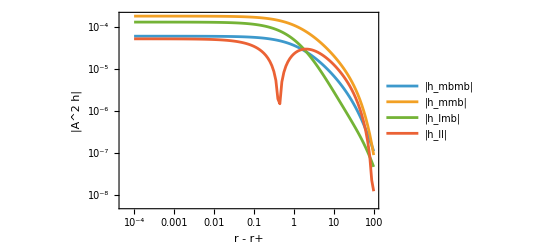

```mathematica
With[{rp = bcmParameters[]["rplus"]},
 ListLogLogPlot[Table[Table[{x, Abs[hComponent[c, rp + x, 21/100]]}, {x, 10^Range[-4, 2, 1/20]}], {c, {"hmbmb", "hmmb", "hlmb", "hll"}}],
  Joined -> True, PlotLegends -> {"|h_mbmb|", "|h_mmb|", "|h_lmb|", "|h_ll|"}, Frame -> True, FrameLabel -> {"r - r+", "|A^2 h|"}, PlotRange -> All]]
```

## Examples: scalar field

Values (physical normalization unless stated; shown to 15 digits, the functions return the full working-precision values):

```mathematica
N[phiCloud[0, 3, 1/2, 0], 15]
N[phiAbs[3, 1/2], 15]
N[Table[fRadial[3, d], {d, 0, 3}], 15]
N[Table[SAngular[1/2, d], {d, 0, 3}], 15]
```

-1.7133377974243×10^-6-4.79709345529713×10^-6 ⅈ

5.09388182302429×10^-6

{3.21860955814641,1.36363464447053,-0.17197538872554,0.0466620459451344}

{-0.299205681018104,0.199491038536398,0.531934932703524,1.06365029512448}

For plots the radial function is tabulated once and interpolated (the series has ~10^4-10^5 terms at working precision); fI[r] = f(r) on r+ < r < rMaxPlot:

```mathematica
With[{p = scalarParameters[]}, rp0 = N[p["rplus"]]; mm0 = p["m"]; om0 = N[p["omega"]]; rm0 = N[p["rminus"]]; nrm0 = N[p["N_Physical"]]];
rMaxPlot = 25/Abs[N[scalarParameters[]["q"]]];          (* |Φ| ~ e^{q r}: 25 e-folds *)
(* nodes from the full-precision r+ (a machine r+ can round below the horizon) *)
fI = With[{rpX = scalarParameters[]["rplus"]}, Interpolation[Table[{N[x], N[fRadial[x]]}, {x, rpX + (rMaxPlot - rpX) Subdivide[0, 1, 600]^2}], InterpolationOrder -> 3]];
SI[c_] := N[SAngular[c]];
```

Radial profile of |Φ| on the equator and on χ = 0.8 (r - r+ on a log axis):

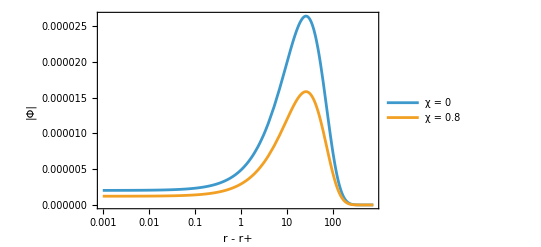

```mathematica
LogLinearPlot[{nrm0 Abs[fI[rp0 + x] SI[0]], nrm0 Abs[fI[rp0 + x] SI[4/5]]}, {x, 10^-3, rMaxPlot - rp0}, PlotRange -> All, Frame -> True,
 FrameLabel -> {"r - r+", "|Φ|"}, PlotLegends -> {"χ = 0", "χ = 0.8"}]
```

|Φ| in the meridional plane (x = r sinθ, z = r cosθ; Boyer-Lindquist-like radius r, black disk r < r+):

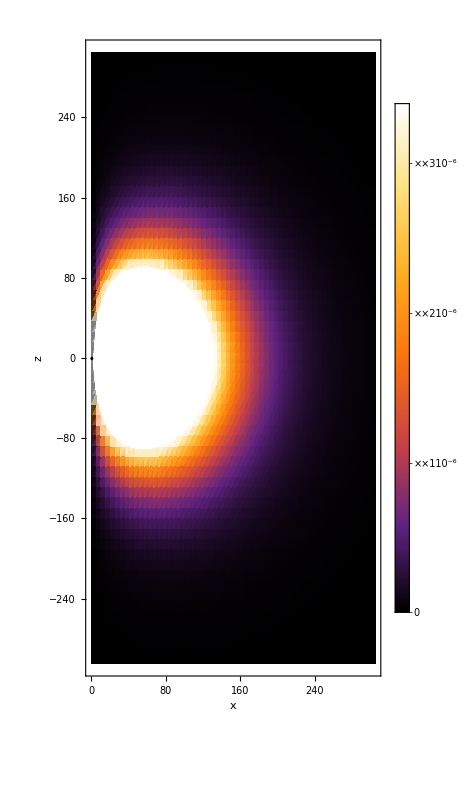

```mathematica
With[{R = rMaxPlot/2.5},
 DensityPlot[With[{r = Sqrt[x^2 + z^2]}, If[r <= rp0, 0, nrm0 Abs[fI[r] SI[z/r]]]], {x, 0, R}, {z, -R, R}, PlotPoints -> 60, AspectRatio -> 2,
  ColorFunction -> "SunsetColors", PlotLegends -> Automatic, FrameLabel -> {"x", "z"}, Epilog -> {Black, Disk[{0, 0}, rp0]}]]
```

Re Φ in the equatorial plane at v = 0 (ingoing coordinates: the phase m φ~ + Θ(r), Θ = ω (r + 2 Log[r - r-]), gives the spiral; in Boyer-Lindquist time slices the pattern is the plain dipole cos(ωt - mφ)):

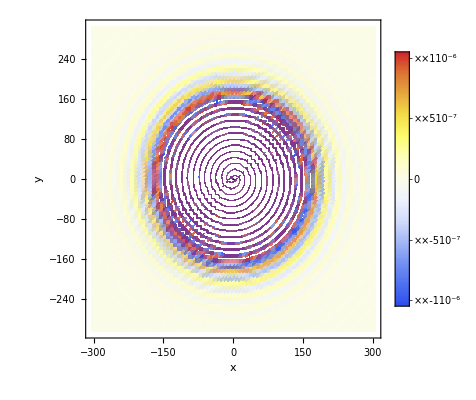

```mathematica
With[{R = rMaxPlot/2.5},
 DensityPlot[With[{r = Sqrt[x^2 + y^2]}, If[r <= rp0, 0, nrm0 fI[r] SI[0] Cos[mm0 ArcTan[x, y] + om0 (r + 2 Log[r - rm0])]]], {x, -R, R}, {y, -R, R}, PlotPoints -> 80,
  ColorFunction -> "TemperatureMap", PlotLegends -> Automatic, FrameLabel -> {"x", "y"}, Epilog -> {Black, Disk[{0, 0}, rp0]}]]
```

Energy density -T^v_v (physical) along the equator, and the cloud mass (a few minutes; equals 10^-4 for the reference run):

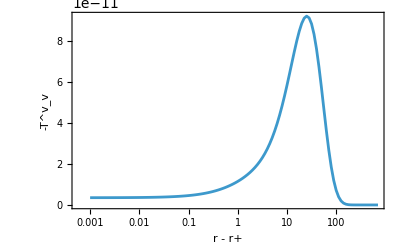

0.0001000000000000000000000057

```mathematica
ListLogLinearPlot[Table[{x, rhoCloud[rp0 + x, 0]}, {x, 10^Range[-3, Log10[rMaxPlot - rp0], 1/20]}], Joined -> True, PlotRange -> All, Frame -> True, FrameLabel -> {"r - r+", "-T^v_v"}]
cloudMass[]
```